```mathematica
copyNotebookDirectory
```

```mathematica
x⇒y//cnf
```

CNF | DNF
¬x∨y | ¬x∨y

```mathematica
beforeCNF
```

```mathematica
z
```

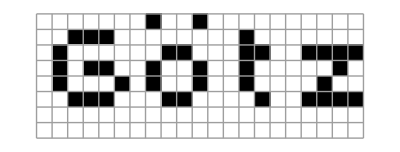
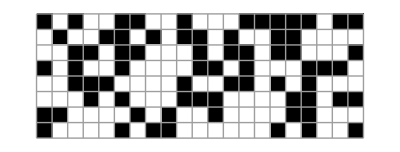
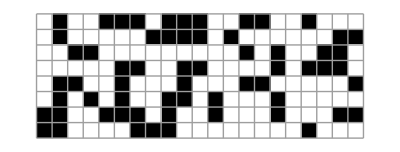
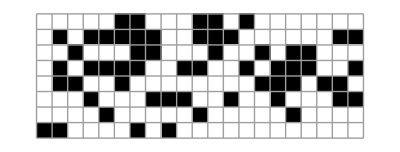
{3.74443,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf4.m"];
LIFE=({{0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 0, 0, 1, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 1, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0, 1, 0, 0, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
(*xPArray=RandomInteger[{0,1},{6,6}];
*)(*updateIJ[xPAay]*)
AbsoluteTiming[{LIFE//plt,updateIJ[LIFE]//lifePlot}]
```

```mathematica
MessageDialog
```

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf3.m"];

output=StringReplace[updateIJF[({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}})],rules];
export="p cnf 48 2015 \n"<>output<>" 0";
ii=Export[NotebookDirectory[]<>"satproblem.txt",export]//Import;
SetDirectory[NotebookDirectory[]];
DeleteFile["satproblem.cnf"];
RenameFile["satproblem.txt","satproblem.cnf"];
ii;
```

```mathematica
Import["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/satproblem1output.txt"]
```

s SATISFIABLE
v -1 2 3 -4 -5 -6 7 -8 -9 0

```mathematica
life33
```

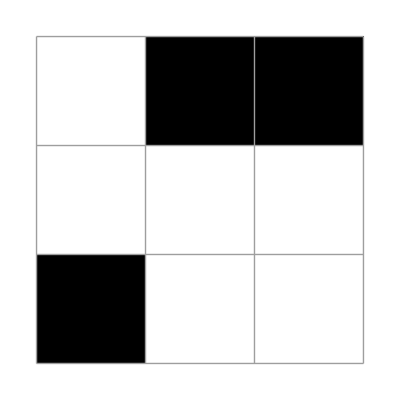
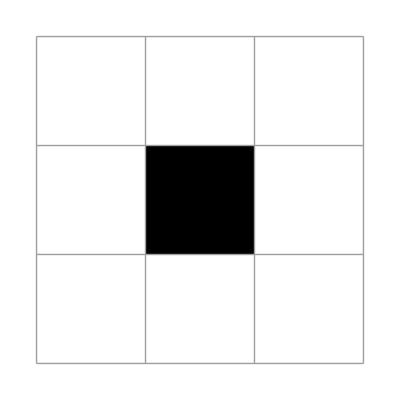

```mathematica
X1=({{0, 1, 1}, {0, 0, 0}, {1, 0, 0}});
plt/@NestList[updateLife[ #]&,
X1,1]
```

```mathematica
|
```

```mathematica
updateIJ[({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})]
```

Set::wrsym: Symbol False is Protected.

General::stop: Further output of Set::wrsym will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in STRING1<>
variables = 48.

SatisfiabilityInstances::bvar: False is not a valid Boolean variable.

RandomChoice::lrwl: The items for choice SatisfiabilityInstances[«1»,{x0[1,1],x0[1,2],x0[1,3],False,x0[2,1],x0[2,2],«36»,x2[3,3],False,False,False,False,False}] should be a list or a rule weights -> choices.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

{{RandomChoice[{}],RandomChoice[{}],RandomChoice[{}],RandomChoice[{}]},{RandomChoice[{}],RandomChoice[{}],RandomChoice[{}],RandomChoice[{}]},{RandomChoice[{}],RandomChoice[{}],RandomChoice[{}],RandomChoice[{}]},{RandomChoice[{}],RandomChoice[{}],RandomChoice[{}],RandomChoice[{}]}}

```mathematica
Clear[i,j,x2];
count[{2,3},{{i,j}[[1]],{i,js}[[2]]},x2]
```

```mathematica
lr
```

and::shdw: Symbol and appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf5.m"]
```

```mathematica
Clear[x0,x1,x2,x3,x4,i,j]CopyToClipboard[BooleanConvert[(and@{Nothing,          ,(x2[i,j]&&count[{2,3},{i,j},x2])~Implies~x3[i,j]
        ,(x2[i,j]&&!count[{2,3},{i,j},x2])~Implies~!x3[i,j]
        ,(!x2[i,j]&&count[{3},{i,j},x2])~Implies~x3[i,j]
        ,(!x2[i,j]&&!count[{3},{i,j},x2])~Implies~!x3[i,j]
}),
"CNF"]];
```